ref/VertexCoordinates

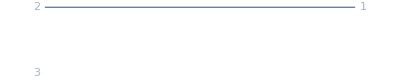

```mathematica
BooleanGraph[And,-Graphics-,-Graphics-,VertexShapeFunction->"Name"]
```

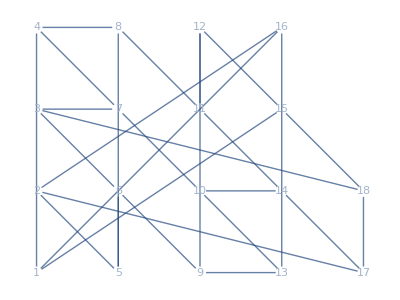

```mathematica
gridLayout[n_]:=Block[{a,b,c},
{a,b,c}={Floor[n^(1/2)],Floor[n/a],Mod[n,a]};
Flatten[Join[Table[{i,j},{i,a},{j,b}],Table[{{a+1,j}},{j,c}]],1]-1
]
GraphPlot[GraphData["PappusGraph"],VertexShapeFunction->"Name",VertexCoordinates->gridLayout[18]]
```

求对两个图进行映射的同构关系：

```mathematica
map=First[Normal[FindGraphIsomorphism[g,h]]]
```

{1→1,2→6,3→4,4→2,5→7,6→5,7→8,8→3}

根据映射关系，对两个图进行突出显示并且添加标签：

```mathematica
a=First/@map;b=Last/@map;
```

```mathematica
highlightGraph[g_,v_]:=HighlightGraph[g,Table[Style[Labeled[v⟦i⟧,v⟦i⟧],ColorData["TemperatureMap"][i/VertexCount[g]]],{i,VertexCount[g]}],VertexSize->Large];
```

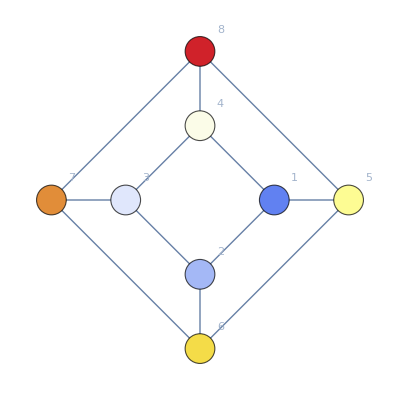
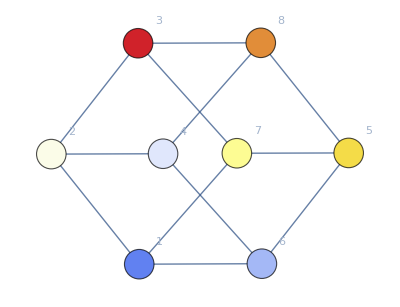

```mathematica
{highlightGraph[g,a],highlightGraph[h,b]}
```

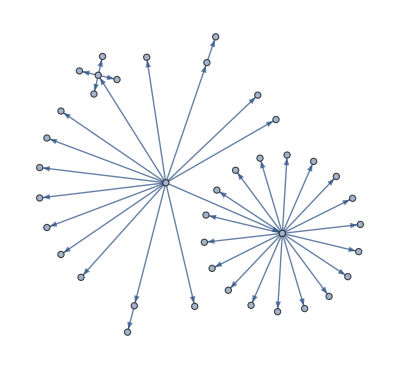

```mathematica
(*文件夹目录的布局 $InstallationDirectory*)
files=Flatten[Rest[NestList[Union[Flatten[Thread[#->FileNames["*",#]]&/@Last/@#]]&,{""->$InstallationDirectory},2]]];
Graph[files, GraphLayout->"BalloonEmbedding"]
```

Johnson Skeleton Graph. Ramsey framework graph